## L-INVARIANT and its Applications

## https : // github.com/PaulChern/L-INVARIANTS

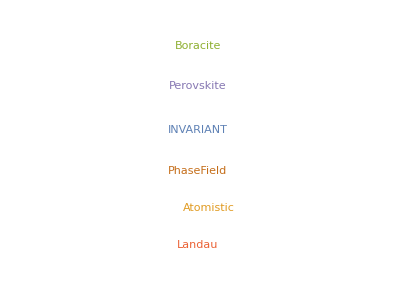

Peng Chen and Sergey Artyukhin

H[ϕ_i,∇_j ϕ_i,∂_t ϕ] or ℒ[ϕ_i,∇_j ϕ_i,∂_t ϕ]

{ϕ_i,∂_t ϕ} are the degree of freedoms  of the system

Motion of equations can be derived from H and L

Phase diagram and transport properties

Reaction path

Domain dynamics

Response to external probes, static and dynamic

The expansion of H and L can be simplified by symmetry adapted basis, such as phonons
L-INVARIANT is a code to do

Model construction

Model fitting

Model solving

DFT modes analysis

DFT modes imposing

Current L-INVARIANT supports Atomistic models very well!
kp, TB and spin models are on the way!

#### In the following, an atomistic model will be taken as an example

#### Example: Perovskite Pm OverBar[3]m

```mathematica
Needs["INVARIANT`"]
```

Reference and P1 structural cif files are the only input files

#### Inputs

```mathematica
Modes="/home/paulchern/Documents/Workshop/Working/CsPbI3/L-INVARIANT/AllModes.Pm-3m.40.cif";
Ref="/home/paulchern/Documents/Workshop/Working/CsPbI3/L-INVARIANT/Pm-3m.vasp.40.cif";
Parent=ImportIsodistortCIF[Modes];
```

#### Reference Structure

```mathematica
LatticeVectorsParent=N[Parent[[6]]/.Parent[[8]]];
Atoms=Parent[[7]];
Wyckoff0=Parent[[10]];
AtomsFrac=CifWyckoffImages[Modes,Wyckoff0];
IsoDim=Parent[[11]];
IsoDispModeMatrix=SparseArray[Thread[Transpose[{Parent[[13]][[1]],Parent[[13]][[2]]}]->Parent[[13]][[3]]],{IsoDim,IsoDim}];
IsoDispModes=Parent[[12]];
```

#### Modes analysis

```mathematica
PopupMenu[Dynamic[mode],IsoDispModes,MenuStyle->"Subsubitem",FieldSize->{140,5}]
```

```mathematica
DistortedFrac=ImposeIsoMode[Wyckoff0,IsoDispModeMatrix,{#1,#2,#3,1}&@@@{mode},8];
IsoModePlotData=Transpose[{Transpose[LatticeVectorsParent].Mod[#,1]&/@Transpose[AtomsFrac][[1]],Transpose[LatticeVectorsParent].#&/@(Transpose[DistortedFrac][[1]]-Transpose[AtomsFrac][[1]]),Transpose[DistortedFrac][[2]]}];
ShowIsoModes[IsoModePlotData]
```

-Graphics3D-

#### INVARIANTS Generator

Get Matrix representation in Landau basis

```mathematica
Timing[OpMatrix=GetOpMatrix[Ref,Wyckoff0,IsoSubDispModeMatrix,IsoDispModes];]
Export["PerovskiteMatrix.dat",OpMatrix,"ExpressionML"];
```

```mathematica
OpMatrix=Import["PerovskiteMatrix.dat","ExpressionML"];
```

Test on single term

```mathematica
invariants=Total[(Subscript[Iso, 61]^2 Subscript[Iso, 62]/.GetIsoTransformRules[#,IsoDispModes])&/@OpMatrix]//Expand
```

0.

```mathematica
ToVar=Thread[(Join[Subscript[Iso, #]&/@Range[61,63],Subscript[Iso, #]&/@Range[100,102]])->(Join[Subscript[ωr, #]&/@{"x","y","z"},Subscript[ωm, #]&/@{"x","y","z"}])]
```

{Iso_61→ωr_x,Iso_62→ωr_y,Iso_63→ωr_z,Iso_100→ωm_x,Iso_101→ωm_y,Iso_102→ωm_z}

```mathematica
invariants/.ToVar
```

```mathematica
128. Subscript[ωr, "x"]^2 Subscript[ωr, "y"]^2+128. Subscript[ωr, "x"]^2 Subscript[ωr, "z"]^2+128. Subscript[ωr, "y"]^2 Subscript[ωr, "z"]^2
```

128. ωr_x^2 ωr_y^2+128. ωr_x^2 ωr_z^2+128. ωr_y^2 ωr_z^2

#### generate interaction n^th order terms of ωr

```mathematica
GetInvariants[Subscript[Iso, #]&/@Range[61,63],8,IsoDispModes,OpMatrix,"ctol"-> 10^-9]/.ToVar//Expand//TableForm
```

1/3 ωr_x^4 ωr_y^2 ωr_z^2+1/3 ωr_x^2 ωr_y^4 ωr_z^2+1/3 ωr_x^2 ωr_y^2 ωr_z^4
1/3 ωr_x^4 ωr_y^4+1/3 ωr_x^4 ωr_z^4+1/3 ωr_y^4 ωr_z^4
1/6 ωr_x^6 ωr_y^2+1/6 ωr_x^2 ωr_y^6+1/6 ωr_x^6 ωr_z^2+1/6 ωr_y^6 ωr_z^2+1/6 ωr_x^2 ωr_z^6+1/6 ωr_y^2 ωr_z^6
ωr_x^8/3+ωr_y^8/3+ωr_z^8/3

```mathematica
Grid[Table[Style[#//Expand,Red,20]&/@(Prepend[GetInvariants[Subscript[Iso, #]&/@Range[61,63],n,IsoDispModes,OpMatrix,"ctol"->10^-7]/.ToVar,n]),{n,Range[1,4]}],Alignment->Left,Frame->All]
```

1 |  | 
2 | ωr_x^2/3+ωr_y^2/3+ωr_z^2/3 | 
3 |  | 
4 | 1/3 ωr_x^2 ωr_y^2+1/3 ωr_x^2 ωr_z^2+1/3 ωr_y^2 ωr_z^2 | ωr_x^4/3+ωr_y^4/3+ωr_z^4/3

#### generate interaction n^th order terms of ωr and ωm

```mathematica
Grid[Table[Style[#//Expand,Red,12]&/@(Prepend[GetInvariants[Join[Subscript[Iso, #]&/@Range[61,63],Subscript[Iso, #]&/@Range[100,102]],n,IsoDispModes,OpMatrix]/.ToVar,n]),{n,Range[1,4]}],Alignment->Left,Frame->All,Spacings->{1,0}]
```

1 |  |  |  |  |  | 
2 | ωr_x^2/3+ωr_y^2/3+ωr_z^2/3 | ωm_x^2/3+ωm_y^2/3+ωm_z^2/3 |  |  |  | 
3 |  |  |  |  |  | 
4 | 1/3 ωr_x^2 ωr_y^2+1/3 ωr_x^2 ωr_z^2+1/3 ωr_y^2 ωr_z^2 | ωr_x^4/3+ωr_y^4/3+ωr_z^4/3 | 1/3 ωm_x^2 ωr_x^2+1/3 ωm_z^2 ωr_y^2+1/3 ωm_y^2 ωr_z^2 | 1/6 ωm_y^2 ωr_x^2+1/6 ωm_z^2 ωr_x^2+1/6 ωm_x^2 ωr_y^2+1/6 ωm_y^2 ωr_y^2+1/6 ωm_x^2 ωr_z^2+1/6 ωm_z^2 ωr_z^2 | 1/3 ωm_x^2 ωm_y^2+1/3 ωm_x^2 ωm_z^2+1/3 ωm_y^2 ωm_z^2 | ωm_x^4/3+ωm_y^4/3+ωm_z^4/3

#### Enough of PmOverBar[3]m, do P4mm

#### Inputs

```mathematica
Modes="/home/paulchern/Documents/Workshop/Working/CsPbI3/L-INVARIANT/AllModes.P4mm.5.cif";
Ref="/home/paulchern/Documents/Workshop/Working/CsPbI3/L-INVARIANT/P4mm.vasp.5.cif";
Parent=ImportIsodistortCIF[Modes];
```

#### Reference Structure

```mathematica
LatticeVectorsParent=N[Parent[[6]]/.Parent[[8]]];
Atoms=Parent[[7]];
Wyckoff0=Parent[[10]];
AtomsFrac=CifWyckoffImages[Modes,Wyckoff0];
IsoDim=Parent[[11]];
IsoSubDispModeMatrix=SparseArray[Thread[Transpose[{Parent[[13]][[1]],Parent[[13]][[2]]}]->Parent[[13]][[3]]],{IsoDim,IsoDim}];
IsoDispModes=Parent[[12]];
```

#### Modes analysis

```mathematica
PopupMenu[Dynamic[mode],IsoDispModes,MenuStyle->"Subsubitem",FieldSize->{140,5}]
```

```mathematica
DistortedFrac=ImposeIsoMode[Wyckoff0,IsoSubDispModeMatrix,{#1,#2,#3,1}&@@@{mode},1];
IsoModePlotData=Transpose[{Transpose[LatticeVectorsParent].Mod[#,1]&/@Transpose[AtomsFrac][[1]],Transpose[LatticeVectorsParent].#&/@(Transpose[DistortedFrac][[1]]-Transpose[AtomsFrac][[1]]),Transpose[DistortedFrac][[2]]}];
ShowIsoModes[IsoModePlotData]
```

-Graphics3D-

Get Matrix representation in Landau basis

```mathematica
OpMatrix=GetOpMatrix[Ref,Wyckoff0,IsoSubDispModeMatrix,IsoDispModes];
```

#### generate interaction n^th order terms of ωr

```mathematica
ToVar=Thread[(Subscript[Iso, #]&/@Range[4,6])->(Subscript[P, #]&/@{"z","x","y"})];
```

```mathematica
GetInvariants[Subscript[Iso, #]&/@Range[4,6],4,IsoDispModes,OpMatrix]/.ToVar//Expand//TableForm
```

P_z^4
P_x^2 P_y^2
1/2 P_x^2 P_z^2+1/2 P_y^2 P_z^2
P_x^4/2+P_y^4/2

```mathematica
Grid[Table[Style[#//Expand,Red,20]&/@(Prepend[GetInvariants[Subscript[Iso, #]&/@Range[4,6],n,IsoDispModes,OpMatrix]/.ToVar,n]),{n,Range[1,6]}],Alignment->Left,Frame->All]
```

1 | P_z |  |  |  |  | 
2 | P_z^2 | P_x^2/2+P_y^2/2 |  |  |  | 
3 | P_z^3 | 1/2 P_x^2 P_z+1/2 P_y^2 P_z |  |  |  | 
4 | P_z^4 | P_x^2 P_y^2 | 1/2 P_x^2 P_z^2+1/2 P_y^2 P_z^2 | P_x^4/2+P_y^4/2 |  | 
5 | P_z^5 | P_x^2 P_y^2 P_z | 1/2 P_x^2 P_z^3+1/2 P_y^2 P_z^3 | 1/2 P_x^4 P_z+1/2 P_y^4 P_z |  | 
6 | P_z^6 | P_x^2 P_y^2 P_z^2 | 1/2 P_x^2 P_z^4+1/2 P_y^2 P_z^4 | 1/2 P_x^4 P_z^2+1/2 P_y^4 P_z^2 | 1/2 P_x^4 P_y^2+1/2 P_x^2 P_y^4 | P_x^6/2+P_y^6/2

#### Enough of Perovskite, dare to do 192-atom cell Boracite (FOverBar[4]3c) with 576 modes?

```mathematica
Import["/home/paulchern/Documents/Workshop/Working/Boracites/paper/fig1/Fig1abc.png"]
```

-Graphics-

#### Inputs

```mathematica
Modes="/home/paulchern/Documents/Workshop/Working/Boracites/L-INVARIANT/PBEsolU/AllModes.F-43c.192.cif";
Ref="/home/paulchern/Documents/Workshop/Working/Boracites/L-INVARIANT/PBEsolU/F-43c.vasp.192.cif";
Parent=ImportIsodistortCIF[Modes];
```

#### Reference Structure

```mathematica
LatticeVectorsParent=N[Parent[[6]]/.Parent[[8]]];
Atoms=Parent[[7]];
Wyckoff0=Parent[[10]];
AtomsFrac=CifWyckoffImages[Modes,Wyckoff0];
IsoDim=Parent[[11]];
IsoSubDispModeMatrix=SparseArray[Thread[Transpose[{Parent[[13]][[1]],Parent[[13]][[2]]}]->Parent[[13]][[3]]],{IsoDim,IsoDim}];
IsoDispModes=Parent[[12]];
```

#### Modes analysis

```mathematica
PopupMenu[Dynamic[mode],IsoDispModes,MenuStyle->"Subsubitem",FieldSize->{140,5}]
```

```mathematica
DistortedFrac=ImposeIsoMode[Wyckoff0,IsoSubDispModeMatrix,{#1,#2,#3,1}&@@@{mode},5];
IsoModePlotData=Transpose[{Transpose[LatticeVectorsParent].Mod[#,1]&/@Transpose[AtomsFrac][[1]],Transpose[LatticeVectorsParent].#&/@(Transpose[DistortedFrac][[1]]-Transpose[AtomsFrac][[1]]),Transpose[DistortedFrac][[2]]}];
ShowIsoModes[IsoModePlotData]
```

-Graphics3D-

Get Matrix representation in Landau basis

```mathematica
Timing[OpMatrix=GetOpMatrix[Ref,Wyckoff0,IsoSubDispModeMatrix,IsoDispModes];]
Export["BoraciteMatrix.dat",OpMatrix,"ExpressionML"];
```

```mathematica
OpMatrix=Import["BoraciteMatrix.dat","ExpressionML"];
```

#### generate interaction n^th order terms of X5 antipolar modes

```mathematica
ToVar=Thread[(Subscript[Iso, #]&/@Range[325,330])->{Subscript[a, 1],Subscript[a, 2],Subscript[b, 1],Subscript[b, 2],Subscript[c, 2],Subscript[c, 1]}];
```

```mathematica
Grid[Table[Style[#//Expand,Red,20]&/@(Prepend[GetInvariants[Subscript[Iso, #]&/@Range[325,330],n,IsoDispModes,OpMatrix]/.ToVar,n]),{n,Range[1,4]}],Alignment->Left,Frame->All]
```

1 |  |  |  |  | 
2 | a_1^2/6+a_2^2/6+b_1^2/6+b_2^2/6+c_1^2/6+c_2^2/6 |  |  |  | 
3 | -1/2 a_1 b_1 c_1+1/2 a_2 b_2 c_2 |  |  |  | 
4 | 1/3 a_1^2 b_2^2+1/3 a_2^2 c_1^2+1/3 b_1^2 c_2^2 | 1/6 a_1^2 b_1^2+1/6 a_2^2 b_2^2+1/6 a_1^2 c_1^2+1/6 b_1^2 c_1^2+1/6 a_2^2 c_2^2+1/6 b_2^2 c_2^2 | 1/3 a_2^2 b_1^2+1/3 b_2^2 c_1^2+1/3 a_1^2 c_2^2 | 1/3 a_1^2 a_2^2+1/3 b_1^2 b_2^2+1/3 c_1^2 c_2^2 | a_1^4/6+a_2^4/6+b_1^4/6+b_2^4/6+c_1^4/6+c_2^4/6

#### Impose modes

## Initializing CsPbI3

```mathematica
dir0="/home/paulchern/Documents/Workshop/Working/CsPbI3/L-INVARIANT/";
SeedSets=<|"cubic-5"->"AllModes.Pm-3m.15.cif","cubic-40"->"AllModes.Pm-3m.40.cif","P4mm"->"AllModes.P4mm.15.cif","Pnma"->"Pnma.vasp.cif"|>;
SymOpFile="/home/paulchern/Documents/Workshop/Working/CsPbI3/ISOTROPY/Pm-3m.vasp.5.cif";
ParentName="cubic-40";
Parent=ImportIsodistortCIF[dir0<>SeedSets[[ParentName]]];
LatticeVectorsParent=N[Parent[[6]]/.Parent[[8]]];
Atoms=Parent[[7]];
Wyckoff0=Parent[[10]];
AtomsFrac=CifWyckoffImages[dir0<>SeedSets[[ParentName]],Wyckoff0];
IsoDim=Parent[[11]];
IsoSubDispModeMatrix=SparseArray[Thread[Transpose[{Parent[[13]][[1]],Parent[[13]][[2]]}]->Parent[[13]][[3]]],{IsoDim,IsoDim}];
IsoDispModes=Parent[[12]];
```

impose modes

```mathematica
DistortedFrac=ImposeIsoMode[Wyckoff0,IsoSubDispModeMatrix,{#1,#2,#3,1}&@@@(IsoDispModes[[#]]&/@{62,63}),1];
IsoModePlotData=Transpose[{Transpose[LatticeVectorsParent].Mod[#,1]&/@Transpose[AtomsFrac][[1]],Transpose[LatticeVectorsParent].#&/@(Transpose[DistortedFrac][[1]]-Transpose[AtomsFrac][[1]]),Transpose[DistortedFrac][[2]]}]
```

{{{0.,0.,0.},{0.,0.,0.},Pb},{{0.,0.,6.23812},{0.,0.,0.},Pb},{{0.,6.23812,0.},{0.,0.,0.},Pb},{{0.,6.23812,6.23812},{0.,0.,0.},Pb},{{6.23812,0.,0.},{0.,0.,0.},Pb},{{6.23812,0.,6.23812},{0.,0.,0.},Pb},{{6.23812,6.23812,0.},{0.,0.,0.},Pb},{{6.23812,6.23812,6.23812},{0.,0.,0.},Pb},{{3.11906,3.11906,3.11906},{0.,0.,0.},Cs},{{3.11906,3.11906,9.35718},{0.,0.,0.},Cs},{{3.11906,9.35718,3.11906},{0.,0.,0.},Cs},{{3.11906,9.35718,9.35718},{0.,0.,0.},Cs},{{9.35718,3.11906,3.11906},{0.,0.,0.},Cs},{{9.35718,3.11906,9.35718},{0.,0.,0.},Cs},{{9.35718,9.35718,3.11906},{0.,0.,0.},Cs},{{9.35718,9.35718,9.35718},{0.,0.,0.},Cs},{{3.11906,0.,0.},{0.,0.,-0.250024},I},{{3.11906,0.,6.23812},{0.,0.,0.250024},I},{{3.11906,6.23812,0.},{0.,0.,0.250024},I},{{3.11906,6.23812,6.23812},{0.,0.,-0.250024},I},{{9.35718,0.,0.},{0.,0.,0.250024},I},{{9.35718,0.,6.23812},{0.,0.,-0.250024},I},{{9.35718,6.23812,0.},{0.,0.,-0.250024},I},{{9.35718,6.23812,6.23812},{0.,0.,0.250024},I},{{0.,3.11906,0.},{0.,0.,0.250024},I},{{0.,3.11906,6.23812},{0.,0.,-0.250024},I},{{0.,9.35718,0.},{0.,0.,-0.250024},I},{{0.,9.35718,6.23812},{0.,0.,0.250024},I},{{6.23812,3.11906,0.},{0.,0.,-0.250024},I},{{6.23812,3.11906,6.23812},{0.,0.,0.250024},I},{{6.23812,9.35718,0.},{0.,0.,0.250024},I},{{6.23812,9.35718,6.23812},{0.,0.,-0.250024},I},{{0.,0.,3.11906},{0.250024,-0.250024,0.},I},{{0.,0.,9.35718},{-0.250024,0.250024,0.},I},{{0.,6.23812,3.11906},{-0.250024,0.250024,0.},I},{{0.,6.23812,9.35718},{0.250024,-0.250024,0.},I},{{6.23812,0.,3.11906},{-0.250024,0.250024,0.},I},{{6.23812,0.,9.35718},{0.250024,-0.250024,0.},I},{{6.23812,6.23812,3.11906},{0.250024,-0.250024,0.},I},{{6.23812,6.23812,9.35718},{-0.250024,0.250024,0.},I}}

save POSCAR

```mathematica
Export["POSCAR",Flatten/@Join[{{"From Mathematica"},{1}},LatticeVectorsParent,{Keys@Counts[DistortedFracᵀ[[-1]]],Values@Counts[DistortedFracᵀ[[-1]]]},{{"Direct"}},({#[[1]],#[[2]]}&/@DistortedFrac)],"Table","FieldSeparators"->"    "];
```

save cif file with "vectors"

```mathematica
Export["Iso-"<>ToString[62]<>".mcif",Flatten/@cif2mcif[dir0<>SeedSets[[ParentName]],62,IsoDispModeMatrix,Wyckoff0],"Table","FieldSeparators"->" "]
```

Iso-62.mcif

#### Modes analysis

```mathematica
modedata["a-a-c+"]=Table[Table[
P16=Import["/home/paulchern/Downloads/PSTRESS/P"<>ToString[i]<>"/CONTCAR","Table"];
{i,ISODISTORT[P16[[3;;5]],Wyckoff0,{P16[[9;;48]],Transpose[Wyckoff0][[2]]}ᵀ,IsoSubDispModeMatrix,IsoDispModesᵀ[[2]]][[mode]][[4]]},{i,Range[0,25]*2}],{mode,{30,39,62,100}}];
```

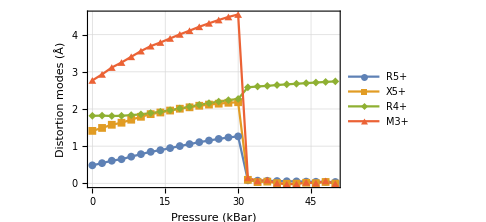

```mathematica
ListPlot[modedata["a-a-c+"],FrameLabel->(Style[#,Black,Bold,12]&/@{"Pressure (kBar)","Distortion modes (Å)"}),AxesStyle->Arrowheads[{0.0,0.05}],PlotRange->{{0,50},Automatic},PlotMarkers->{Automatic, 8},ImageSize->Medium,Joined->True,Frame->True,GridLines->Automatic,PlotLegends->{"R5+","X5+","R4+","M3+"}]
```

#### Model Solving

```mathematica
Import["/home/paulchern/Documents/Workshop/Working/Boracites/paper/fig3/fig3.png"]
```

-Graphics-

#### Nudged Elastic Bands

```mathematica
Import["/home/paulchern/Documents/Workshop/Working/Boracites/paper/fig2/fig2.png"]
```

-Graphics-

```mathematica
Import["/home/paulchern/PES_+a1+a2_+b1+b2_1.gif","Animation"]
```